```mathematica
raw=OpenRead["C:\\MyFiles\\MathmaticaWorkspace\\reviews.csv"];
data=Map[StringSplit[#,"|"]&,ReadList[raw,String]]
test=ToLowerCase[Take[data,{1,-1,5}]]
train=ToLowerCase[Drop[data,{1,-1,5}]]
```

{{label,text},399999,{negative,Comedy Scene, and Not Heard: This DVD will be a disappointment if you get it hoping to see some substantial portion of the acts of the various comics listed on the cover. All you get here are snippets of performance, at best. The rest is just loose-leaf reminiscence about the good old days in Boston…e)perpetrated - back then. But you had to have been there to appreciate all the basically good ol' boy camaraderie. If you weren't actually a part of that scene, all this joshing and jostling will fall flat.If you want to actually hear some of these comics' routines - you will have to look elsewhere.}}
 |  |  |  |

{{label,text},79999,{negative,comedy scene, and not heard: this dvd will be a disappointment if you get it hoping to see some substantial portion of the acts of the various comics listed on the cover. all you get here are snippets of performance, at best. the rest is just loose-leaf reminiscence about the good old days in boston…e)perpetrated - back then. but you had to have been there to appreciate all the basically good ol' boy camaraderie. if you weren't actually a part of that scene, all this joshing and jostling will fall flat.if you want to actually hear some of these comics' routines - you will have to look elsewhere.}}
 |  |  |  |

{{positive,great cd: my lovely pat has one of the great voices of her generation. i have listened to this cd for years and i still love it. when i'm in a good mood it makes me feel better. a bad mood just evaporates like sugar in the rain. this cd just oozes life. vocals are jusat stuunning and lyrics just kill. one of life's hidden gems. this is a desert isle cd in my book. why she never made it big is just beyond me. everytime i play this, no matter black, white, young, old, male, female everybody says one thing "who was that singing ?"},319998,{positive,classic jessica mitford: this is …n, and a complete delight to read.}}
 |  |  |  |

```mathematica
(* This conmmeted part is the code that preprocess the training data. The reason we comment it out is that by reading the existing file is much faster than run it again.
If you want to run this part please cancle tha comment and change the output file path and the path parameter of OpenRead *)

(*
count=0
words=<||>
counts=<||>
For[i=1,i<Length[train]+1,i++,
For[j=1,j<Length[train[[i]]]+1,j++,
train[[i]][[2]]=StringReplace[train[[i]][[2]],PunctuationCharacter->" "];
strs=StringSplit[train[[i]][[2]], " "];
For[k=1,k<Length[strs],k++,
count=count+1;
Lookup[words,strs[[k]], AssociateTo[words, strs[[k]]->0]];
Lookup[counts,strs[[k]], AssociateTo[counts, strs[[k]]->0]];
AssociateTo[counts,strs[[k]]->counts[[strs[[k]]]]+1];
If[train[[i]][[1]]=="positive",
AssociateTo[words,strs[[k]]->words[[strs[[k]]]]+1],
AssociateTo[words,strs[[k]]->words[[strs[[k]]]]-1]
];
]
]
]
fout=OpenWrite["C:\\MyFiles\\MathmaticaWorkspace\\out.csv"]
keys=Keys[words]
For[i=1,i<Length[keys]+1,i++,
AssociateTo[words,keys[[i]]->{words[[keys[[i]]]],counts[[keys[[i]]]]}];
str = keys[[i]]<>"|"<>ToString[words[[keys]][[i]][[1]]]<>"/"<>ToString[words[[keys]][[i]][[2]]]<>"\n";
WriteString[fout,str];
]
Close[fout]
*)

(* This part is the part we can read the output file *)
raw=OpenRead["https://github.com/TheEler/csci561-dataset3/files/1143663/wordWithCount.txt"];
wnw=Map[StringSplit[#,"|"]&,ReadList[raw,String]]
```

{{great,104654,188614},{cd,14620,72072},{ ,-303312,6934528},{my,19222,330458},{lovely,1300,2736},{pat,74,718},{has,11902,137742},{one,-3836,237068},{of,12008,1008212},{the,-133074,2556582},{voices,486,2166},{her,10354,84274},{generation,344,2136},{i,-139250,1482982},223749,{enstranged,2,2},{diairies,2,2},{tvd,2,2},{derailes,-2,2},{caliming,-2,2},{acoomodate,-2,2},{financil,-2,2},{gabay,-2,2},{landingwhere,-2,2},{someonesaying,-2,2},{anamorphics,2,2},{18w,-2,2},{tildsmen,-2,2}}
 |  |  |  |

```mathematica
pairs=<||>
For[i=1,i<Length[wnw]+1,i++,pairs[wnw[[i]][[1]]]=(ToExpression[wnw[[i]][[2]]])]
```

<||>

<|great→104654,cd→14620, →-303312,my→19222,lovely→1300,pat→74,has→11902,one→-3836,of→12008,the→-133074,voices→486,her→10354,generation→344,i→-139250,have→-17742,listened→434,to→-61028,this→-44702,for→16588,years→7918,and→83814,still→5792,love→43604,it→-76148,223729,capsizings→2,extrabiblical→-2,intriqed→-2,fengshui→2,coustemer→-2,2002pulp→-2,adurable→-2,ltm225w→-2,ygg→2,componentry→-2,enstranged→2,diairies→2,tvd→2,derailes→-2,caliming→-2,acoomodate→-2,financil→-2,gabay→-2,landingwhere→-2,someonesaying→-2,anamorphics→2,18w→-2,tildsmen→-2|>
 |  |  |  |

```mathematica
pairs=Sort[pairs,Abs[#1]>Abs[#2]&]
```

<| →-303312,not→-164030,i→-139250,the→-133074,great→104654,t→-98576,was→-88470,and→83814,it→-76148,to→-61028,but→-46956,this→-44702,love→43604,that→-42242,no→-40468,best→38832,don→-36086,would→-35414,money→-34436,is→32062,waste→-29736,be→-29112,on→-28964,bad→-28890,good→28778,if→-27706,223724,uppers→0,alien→0,agricultural→0,jamas→0,linus→0,launch→0,corsets→0,dredg→0,chanson→0,laiden→0,chillingworth→0,stifled→0,dimmesdale→0,prynne→0,tendencies→0,gud→0,priori→0,kurdish→0,120lbs→0,crunched→0,frosts→0,owns→0,howeve→0,assails→0,powerex→0,isle→0|>
 |  |  |  |

```mathematica
keys = Keys[pairs]
vals = Values[pairs]
keys=keys[[1;;1200]]
```

{ ,not,i,the,great,t,was,and,it,to,but,this,love,that,no,best,don,would,money,is,waste,be,on,bad,good,if,they,just,do,excellent,even,after,buy,or,well,had,easy,too,did,223698,viewpoint,primary,bootstrap,knievel,w80,banter,mortage,sterling,beneath,cutltural,lakein,architect,husbandand,uppers,alien,agricultural,jamas,linus,launch,corsets,dredg,chanson,laiden,chillingworth,stifled,dimmesdale,prynne,tendencies,gud,priori,kurdish,120lbs,crunched,frosts,owns,howeve,assails,powerex,isle}
 |  |  |  |

{-303312,-164030,-139250,-133074,104654,-98576,-88470,83814,-76148,-61028,-46956,-44702,43604,-42242,-40468,38832,-36086,-35414,-34436,32062,-29736,-29112,-28964,-28890,28778,-27706,-27162,-25286,-25284,24096,-23996,-23844,-23326,-22876,22810,-21800,21094,-20818,-20594,-19928,-19588,-19584,19222,-18564,18542,18452,-18354,-18344,-18028,-18010,-17742,-17582,-17470,-17350,17298,-17008,16588,16144,-16076,-15990,-15926,-15590,15470,15066,-14962,-14636,14620,14328,14104,-14050,13746,13696,-13696,223630,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
 |  |  |  |

{ ,not,i,the,great,t,was,and,it,to,but,this,love,that,no,best,don,would,money,is,waste,be,on,bad,good,if,they,just,do,excellent,even,after,buy,or,well,had,easy,too,did,product,disappointed,there,my,get,s,album,poor,off,didn,only,have,worst,at,what,read,nothing,for,a,work,were,out,then,wonderful,his,boring,could,cd,you,fun,because,life,perfect,doesn,same,highly,your,music,so,terrible,in,favorite,must,bought,of,has,horrible,book,should,amazing,amazon,2,tried,return,about,as,awesome,recommend,reviews,like,works,never,her,nice,better,something,why,movie,much,does,very,disappointing,loved,who,back,item,beautiful,our,save,months,when,little,1,quality,any,instead,thing,time,got,maybe,songs,cheap,enjoyed,up,another,story,awful,also,loves,anything,poorly,price,made,years,from,wrong,two,received,thought,me,author,problem,junk,he,try,always,disappointment,broke,m,returned,plot,trying,song,classic,family,unfortunately,ok,an,however,unit,world,every,series,minutes,going,before,worse,3,worked,support,enjoy,useless,pages,plastic,she,half,piece,buying,fantastic,unless,company,with,dvd,purchased,wouldn,please,still,sent,least,guess,pay,ordered,garbage,than,customer,each,sorry,star,definitely,other,completely,which,box,anyone,those,want,makes,collection,especially,wasn,bit,either,stopped,rock,can,stupid,happy,phone,actually,working,less,job,idea,said,away,make,own,give,stay,version,am,couldn,most,called,heart,seems,gives,else,service,send,went,someone,young,cannot,crap,warranty,refund,few,history,been,dont,weak,hoping,isn,seemed,avoid,weeks,believe,wasted,rather,where,beware,way,bother,broken,left,paid,pleased,software,might,one,live,overall,annoying,defective,spend,trash,friends,supposed,total,d,ve,let,won,battery,thinking,truly,reason,replacement,enjoyable,over,yet,fast,everyone,description,returning,show,simple,hard,original,liked,stories,both,picture,us,failed,until,listen,film,many,by,used,order,solid,along,says,gift,unique,incredible,lot,stick,him,say,kids,spent,sucks,true,apart,point,looked,hate,happened,write,greatest,season,started,seller,barely,products,enough,review,writing,its,entertaining,dull,cost,brand,design,low,line,acting,outstanding,know,slow,heard,purchase,call,shows,gave,finish,worthless,10,thank,tracks,already,told,fan,band,lasted,okay,attempt,perfectly,skip,expected,glad,children,zero,helps,sell,their,name,christmas,people,batteries,ridiculous,month,again,recommended,complete,cover,track,within,keeps,mistake,errors,fit,computer,funny,difficult,powerful,lame,helped,fact,shame,war,itself,bottom,favorites,took,impossible,looks,misleading,are,feel,we,paper,screen,basically,stuck,sure,care,last,superb,hours,first,son,lack,home,machine,though,comfortable,hold,man,lives,guitar,provides,brings,water,takes,sweet,expecting,rip,joke,personal,charge,brilliant,excited,fits,totally,0,30,title,end,wanted,ended,use,week,voice,replace,page,albums,fans,jazz,buyer,perhaps,turned,sturdy,died,really,properly,character,thin,them,apparently,listening,friend,reading,probably,cut,turn,looking,quick,informative,beautifully,sony,predictable,cool,short,fix,mean,felt,shipping,re,almost,missing,books,flat,quite,threw,such,obviously,now,rating,6,dead,longer,daughter,soul,fascinating,big,none,needed,lost,flimsy,night,hour,may,journey,school,keep,device,nor,fell,learning,oh,mess,need,exactly,error,characters,repair,adventure,helpful,badly,extremely,twice,rest,player,printer,terrific,seem,thanks,tech,lots,day,set,video,00,decent,opened,super,example,contacted,tool,information,confusing,strong,store,second,condition,found,frustrating,20,model,kept,human,style,entire,rocks,50,addition,early,actual,plain,case,mediocre,complaint,everything,coffee,action,package,website,husband,replaced,problems,country,manufacturer,likes,fails,simply,guy,luck,warning,mind,hilarious,correct,huge,camera,windows,agree,content,blues,fabulous,de,beat,reference,saying,modern,dissapointed,wow,go,receive,neither,number,dumb,pathetic,resource,seriously,playing,run,sold,material,contact,important,drive,15,expect,some,throw,print,noise,based,false,tale,tell,lyrics,self,quit,reviewers,hooked,script,hopes,art,american,edition,ages,fine,value,obvious,lousy,expensive,except,fresh,parts,here,hype,email,today,sex,living,clear,humor,sad,part,pointless,eyes,lacks,mix,packaging,three,hardly,shallow,main,handy,sadly,rent,deep,heavy,falls,cheaply,claims,think,through,old,smooth,remember,masterpiece,wait,days,memories,wonderfully,dance,positive,lacking,purchasing,getting,bunch,workout,kind,dialogue,musical,introduction,card,bored,fake,ripped,site,decided,hated,joy,easier,includes,easily,become,mother,nicely,effort,silly,moving,dollars,haven,mention,ever,making,understanding,mystery,anymore,age,online,advice,sending,ruined,tedious,delightful,during,father,waiting,vocals,hits,everyday,group,cable,interested,these,open,unable,refreshing,didnt,real,appears,wonder,button,handle,inspiring,audio,under,listed,into,designed,elsewhere,guide,god,response,being,wrote,hp,appreciate,base,e,copy,sometimes,comes,suggest,variety,bucks,couple,selling,suppose,talking,stinks,instructions,bible,house,all,ink,rare,covers,although,later,john,daily,mail,tries,summer,lovely,reader,parents,motor,bonus,pleasure,favor,concept,forced,clean,pass,switch,static,brought,internet,rate,laugh,xp,advertised,gone,step,touching,spiritual,detailed,code,essential,issue,result,premise,break,practical,gem,miss,surprised,smell,kindle,credit,artist,painful,major,satisfied,things,wasting,bland,perspective,pc,seconds,inside,look,publisher,needs,99,toy,nearly,excuse,students,room,100,town,loose,due,disgusting,black,damaged,girl,long,remove,nowhere,tells,travel,constantly,thoroughly,scenes,previous,exciting,plays,spirit,wife,definately,whole,terribly,clock,cute,holds,blah,attempts,illustrations,tunes,insight,mine,beauty,repetitive,costs,concert,future,noticed,stars,durable,cracked,study,times,understand,stated,burned,connection,web,average,allows,plenty,leaks,disc,debut,spending,etc,crappy,mom,learn,lid,enjoys,packed,otherwise,shut,authors,dream,figure,realistic,find,rated,potential,substance,year,bring,uncomfortable,ship,china,sounded,sister,third,soundtrack,against,dangerous,timeless,worth,opinion,ways,sounds,will,treat,explains,delicious,bass,redeeming,eye,load,start,failure,plugged,correctly,text,suck,matter,outdated,unhappy,emotional,traditional,master,paying,provoking,download,yourself,alot,word,unlike,performance,course,carry,editor,editing,features,romantic,customers,edited,share,treasure,program,done,saw,finest,historical,adults,lens,tape,sucked,biggest,pleasantly,compatible,depressing,non,photo,comprehensive,free,boy,came,manual,horribly,quiet,growing,sort,wanting,disapointed,delight,century,update,insult,label,relate,overrated,disk,quickly,dr,enjoying,cast,installed,overpriced,hole,between,stunning,lovers,clearly,follow,whatsoever,falling,captures,ugh,holes,hoped,loving,unrealistic,checked,amazed,piano,honestly,magic,recipes,pictured,burn,novel,played,ride,stores,uninteresting,ashamed,childhood,ability,frankly,control,trite,therefore,performances,sense,drivel,reviewer,fail,recording,awsome,talk,relationship,charger,upset,drama,pieces,doesnt,intense,remarkable,cookbook,exchange,wear,twists,king,blu,chapters,yes,insightful,sick,white,published,fooled,image,shouldn,era,surprise,figured,inaccurate,signal,ugly,beyond,inspired,finds,irritating,cheesy,buttons,weren,charming,chapter,system,unusable,emotions,trip,recently,charged,mood,gorgeous,incorrect,trust,vendor,five,haunting,bottle,below,means,genius,12,several,ipod,hassle,boys,realized,throwing,calls,brother,deal,y,began,ease,harry,filter,adventures,various,tiny,pop,alive,add,edge,microsoft,somewhere,file,city,beats,la,complex,styles,function,familiar,minor,compact,pump,down,waited,among,engaging,usb,mentioned,shipped,pretentious,romance,exceptional,leaking,cooking,offers,throughout,hair,lover,limited,beginning,policy,empty,dvds,display,leak,printed,middle,able,fault,dollar,sale,range,advertising,user,extended,info,recomend,faulty,asked,supposedly,inferior,western,anti}

```mathematica
encoder=NetEncoder[{"Tokens",keys}]
wordBoundary=Length[keys]+1
```

NetEncoder[<>]

1201

```mathematica
(* Get the indices of words appeared in training data and remove the invalid indices for NN *)
NNindex ={}
For[i=1,i<Length[train]+1,i++,AppendTo[NNindex,encoder[train[[i]][[2]]]]]
For[i=1,i<Length[NNindex]+1,i++,For[j=1,j<Length[NNindex[[i]]]+1,j++,If[NNindex[[i]][[j]]==wordBoundary,(NNindex[[i]]=Delete[NNindex[[i]],j];j--)]]]
(* Get the training values *)
NNtrainVals={}
For[i=1,i<Length[train]+1,i++,AppendTo[NNtrainVals,train[[i]][[1]]]]
(* Generate the input vector of training data *)
NNvector={}
For[i=1,i<Length[NNindex]+1,i++,AppendTo[NNvector,ConstantArray[0,wordBoundary-1]]]
For[i=1,i<Length[NNindex]+1,i++,For[j=1,j<Length[NNindex[[i]]]+1,j++,NNvector[[i]]=ReplacePart[NNvector[[i]],NNindex[[i]][[j]]->1]]]
```

{}

{}

{}

```mathematica
(* Get the indices of words appeared in training data and remove the invalid indices for RF *)
RFindex ={}
For[i=1,i<12000+1,i++,AppendTo[RFindex,encoder[train[[i]][[2]]]]]
For[i=1,i<Length[RFindex]+1,i++,For[j=1,j<Length[RFindex[[i]]]+1,j++,If[RFindex[[i]][[j]]==wordBoundary,(RFindex[[i]]=Delete[RFindex[[i]],j];j--)]]]
(* Get the training values *)
RFtrainVals={}
For[i=1,i<12000+1,i++,AppendTo[RFtrainVals,train[[i]][[1]]]]
(* Generate the input vector of training data *)
RFvector={}
For[i=1,i<Length[RFindex]+1,i++,AppendTo[RFvector,ConstantArray[0,wordBoundary-1]]]
For[i=1,i<Length[RFindex]+1,i++,For[j=1,j<Length[RFindex[[i]]]+1,j++,RFvector[[i]]=ReplacePart[RFvector[[i]],RFindex[[i]][[j]]->1]]]
```

{}

{}

{}

«1 more identical outputs»

```mathematica
(* Get the indices of words appeared in training data and remove the invalid indices for LogisticRegression *)
Lindex ={}
For[i=1,i<Length[train]+1,i++,AppendTo[Lindex,encoder[train[[i]][[2]]]]]
For[i=1,i<Length[Lindex]+1,i++,For[j=1,j<Length[Lindex[[i]]]+1,j++,If[Lindex[[i]][[j]]==wordBoundary,(Lindex[[i]]=Delete[Lindex[[i]],j];j--)]]]
(* Get the training values *)
LtrainVals={}
For[i=1,i<Length[train]+1,i++,AppendTo[LtrainVals,train[[i]][[1]]]]
(* Generate the input vector of training data *)
Lvector={}
For[i=1,i<Length[Lindex]+1,i++,AppendTo[Lvector,ConstantArray[0,wordBoundary-1]]]
For[i=1,i<Length[Lindex]+1,i++,For[j=1,j<Length[Lindex[[i]]]+1,j++,Lvector[[i]]=ReplacePart[Lvector[[i]],Lindex[[i]][[j]]->1]]]
```

{}

{}

{}

```mathematica
cNN=Classify[NNvector->NNtrainVals,Method->{"NeuralNetwork","HiddenLayers"->20,"PerformanceGoal"->"Quality"}]
```

ClassifierFunction[…]

```mathematica
cRF=Classify[RFvector->RFtrainVals,Method->{"RandomForest","VariableSampleSize"->3,"TreeNumber"->30}]
```

ClassifierFunction[…]

```mathematica
cL=Classify[Lvector->LtrainVals,Method->"LogisticRegression"]
```

ClassifierFunction[…]

{}

{}

{}

0.870575

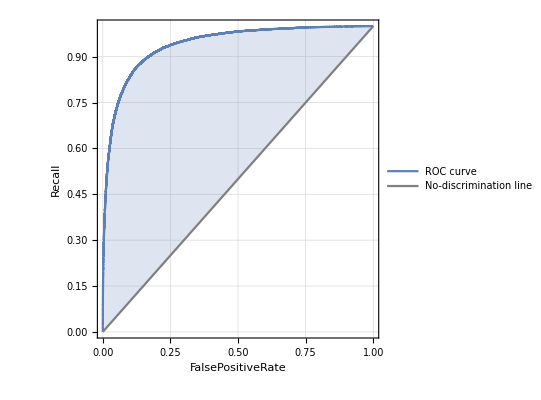
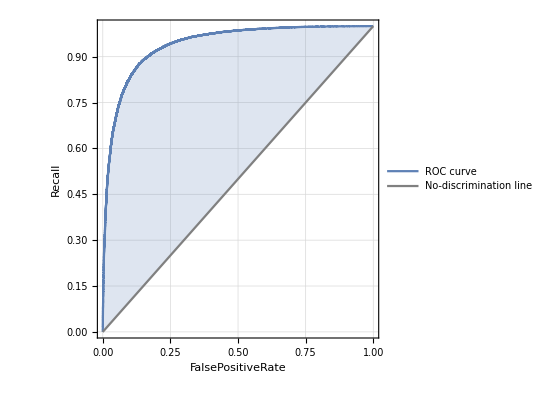
<|negative→-Graphics-,positive→-Graphics-|>

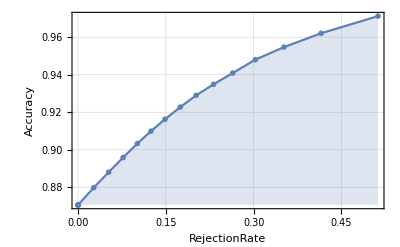

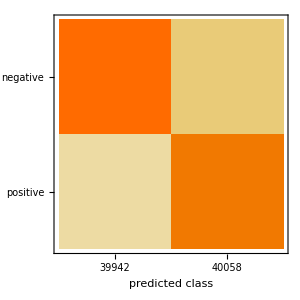

<|negative→0.868102,positive→0.873072|>

<|negative→0.873492,positive→0.867667|>

```mathematica
(* Get the indices of words appeard in test data and remove the invalid indices for NN *)
NNtestIndex ={}
For[i=2,i<Length[test]+1,i++,AppendTo[NNtestIndex,encoder[test[[i]][[2]]]]]
For[i=1,i<Length[NNtestIndex]+1,i++,For[j=1,j<Length[NNtestIndex[[i]]]+1,j++,If[NNtestIndex[[i]][[j]]==wordBoundary,(NNtestIndex[[i]]=Delete[NNtestIndex[[i]],j];j--)]]]
(* enerate the input vector of training data of test data *)
NNtestVector={}
For[i=1,i<Length[NNtestIndex]+1,i++,AppendTo[NNtestVector,ConstantArray[0,wordBoundary-1]]]
For[i=1,i<Length[NNtestIndex]+1,i++,For[j=1,j<Length[NNtestIndex[[i]]]+1,j++,NNtestVector[[i]]=ReplacePart[NNtestVector[[i]],NNtestIndex[[i]][[j]]->1]]]
NNtestValues={}
For[i=2,i<Length[NNtestIndex]+2,i++,AppendTo[NNtestValues,test[[i]][[1]]]]
ClassifierMeasurements[cNN,NNtestVector-> NNtestValues,"Accuracy"]
ClassifierMeasurements[cNN,NNtestVector-> NNtestValues,"ROCCurve"]
ClassifierMeasurements[cNN,NNtestVector-> NNtestValues,"AccuracyRejectionPlot"]
ClassifierMeasurements[cNN,NNtestVector-> NNtestValues,"ConfusionMatrixPlot"]
ClassifierMeasurements[cNN,NNtestVector-> NNtestValues,"Recall"]
ClassifierMeasurements[cNN,NNtestVector-> NNtestValues,"Precision"]
```

{}

{}

{}

0.772667

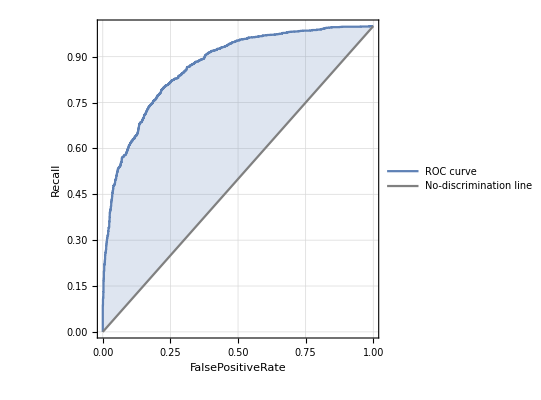
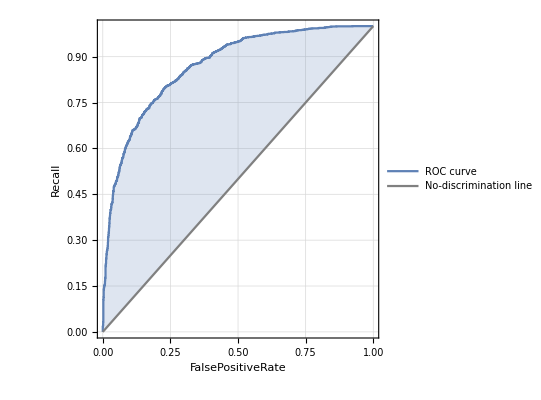
<|negative→-Graphics-,positive→-Graphics-|>

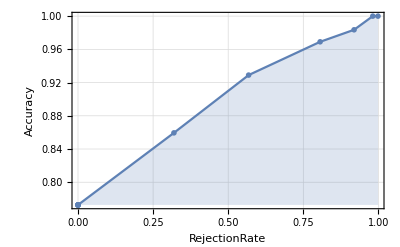

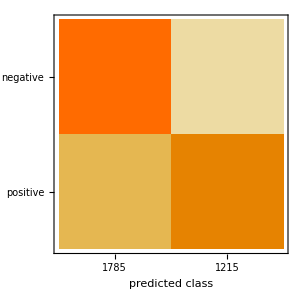

<|negative→0.87138,positive→0.675908|>

<|negative→0.72493,positive→0.842798|>

```mathematica
(* Get the indices of words appeard in test data and remove the invalid indices for RF*)
RFtestIndex ={}
For[i=2,i<3001+1,i++,AppendTo[RFtestIndex,encoder[test[[i]][[2]]]]]
For[i=1,i<Length[RFtestIndex]+1,i++,For[j=1,j<Length[RFtestIndex[[i]]]+1,j++,If[RFtestIndex[[i]][[j]]==wordBoundary,(RFtestIndex[[i]]=Delete[RFtestIndex[[i]],j];j--)]]]
(* enerate the input vector of training data of test data *)
RFtestVector={}
For[i=1,i<Length[RFtestIndex]+1,i++,AppendTo[RFtestVector,ConstantArray[0,wordBoundary-1]]]
For[i=1,i<Length[RFtestIndex]+1,i++,For[j=1,j<Length[RFtestIndex[[i]]]+1,j++,RFtestVector[[i]]=ReplacePart[RFtestVector[[i]],RFtestIndex[[i]][[j]]->1]]]
RFtestValues={}
For[i=2,i<Length[RFtestIndex]+2,i++,AppendTo[RFtestValues,test[[i]][[1]]]]
ClassifierMeasurements[cRF,RFtestVector-> RFtestValues,"Accuracy"]
ClassifierMeasurements[cRF,RFtestVector-> RFtestValues,"ROCCurve"]
ClassifierMeasurements[cRF,RFtestVector-> RFtestValues,"AccuracyRejectionPlot"]
ClassifierMeasurements[cRF,RFtestVector-> RFtestValues,"ConfusionMatrixPlot"]
ClassifierMeasurements[cRF,RFtestVector-> RFtestValues,"Recall"]
ClassifierMeasurements[cRF,RFtestVector-> RFtestValues,"Precision"]
```

{}

{}

{}

0.882763

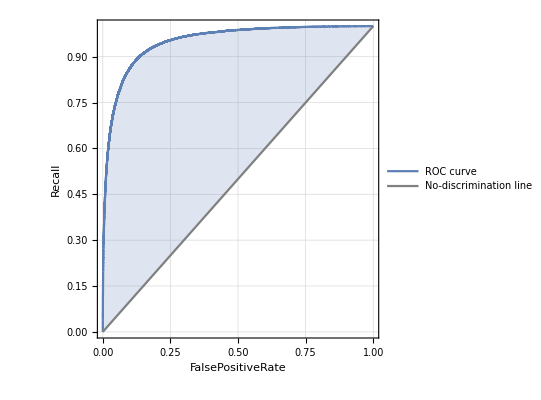
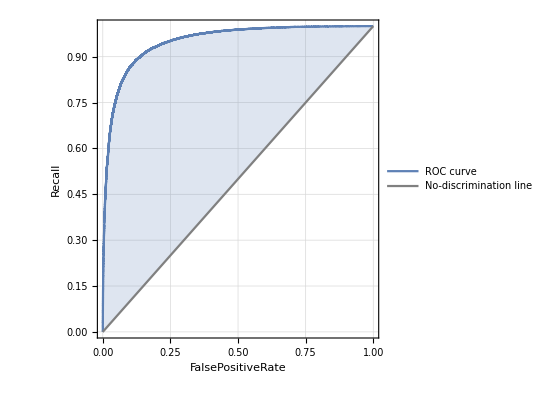
<|negative→-Graphics-,positive→-Graphics-|>

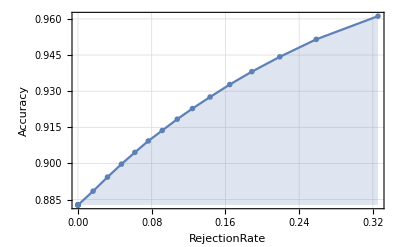

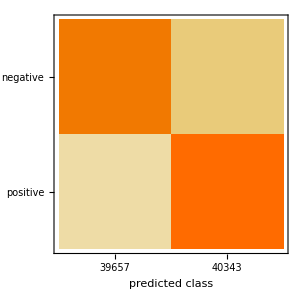

<|negative→0.876686,positive→0.888897|>

<|negative→0.888469,positive→0.877153|>

```mathematica
(* Get the indices of words appeard in test data and remove the invalid indices for Logistic Regression *)
LtestIndex ={}
For[i=2,i<Length[test]+1,i++,AppendTo[LtestIndex,encoder[test[[i]][[2]]]]]
For[i=1,i<Length[LtestIndex]+1,i++,For[j=1,j<Length[LtestIndex[[i]]]+1,j++,If[LtestIndex[[i]][[j]]==wordBoundary,(LtestIndex[[i]]=Delete[LtestIndex[[i]],j];j--)]]]
(* enerate the input vector of training data of test data *)
LtestVector={}
For[i=1,i<Length[LtestIndex]+1,i++,AppendTo[LtestVector,ConstantArray[0,wordBoundary-1]]]
For[i=1,i<Length[LtestIndex]+1,i++,For[j=1,j<Length[LtestIndex[[i]]]+1,j++,LtestVector[[i]]=ReplacePart[LtestVector[[i]],LtestIndex[[i]][[j]]->1]]]
LtestValues={}
For[i=2,i<Length[LtestIndex]+2,i++,AppendTo[LtestValues,test[[i]][[1]]]]
ClassifierMeasurements[cL,LtestVector-> LtestValues,"Accuracy"]
ClassifierMeasurements[cL,LtestVector-> LtestValues,"ROCCurve"]
ClassifierMeasurements[cL,LtestVector-> LtestValues,"AccuracyRejectionPlot"]
ClassifierMeasurements[cL,LtestVector-> LtestValues,"ConfusionMatrixPlot"]
ClassifierMeasurements[cL,LtestVector-> LtestValues,"Recall"]
ClassifierMeasurements[cL,LtestVector-> LtestValues,"Precision"]
```

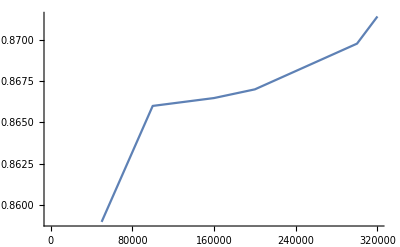

```mathematica
(* Here is the graph of the accuracy of Neural Network with increasing training data, the data comes from several times testing *)
ListLinePlot[{{50000,0.859},{100000,0.866},{160000,0.866475},{200000,0.867},{300000,0.86976},{320000,0.8714}}]
```

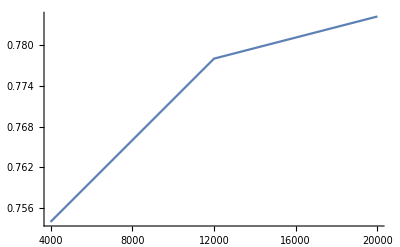

```mathematica
(* Here is the graph of the accuracy of Random Forest with increasing training data, the data comes from several times testing *)
ListLinePlot[{{4000,0.754},{12000,0.778},{20000,0.7842}}]
```

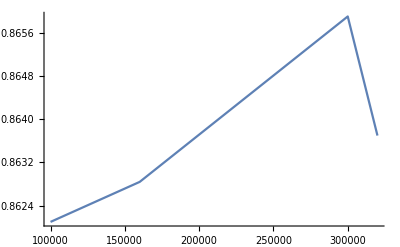

```mathematica
(* Here is the graph of the positive Precision of Neural Network with increasing training data, the data comes from several times testing *)
ListLinePlot[{{100000,0.8621},{160000,0.86284},{300000,0.8659},{320000,0.863697}}]
```

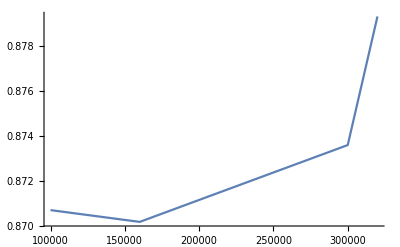

```mathematica
(* Here is the graph of the negative Precision of Neural Network with increasing training data, the data comes from several times testing *)
ListLinePlot[{{100000,0.8707},{160000,0.870175},{300000,0.8736},{320000,0.879332}}]
```

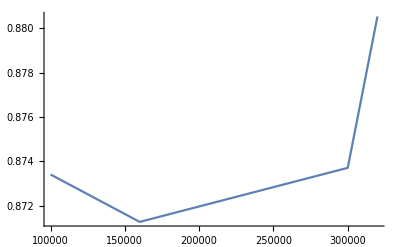

```mathematica
(* Here is the graph of the positive Recall of Neural Network with increasing training data, the data comes from several times testing *)
ListLinePlot[{{100000,0.8734},{160000,0.87126},{300000,0.8737},{320000,0.880533}}]
```

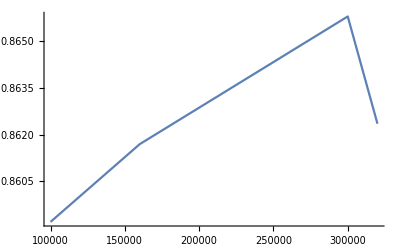

```mathematica
(* Here is the graph of the negative Recall of Neural Network with increasing training data, the data comes from several times testing *)
ListLinePlot[{{100000,0.8592},{160000,0.861697},{300000,0.8658},{320000,0.862354}}]
```

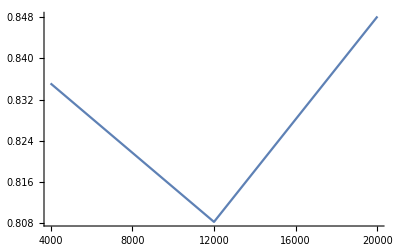

```mathematica
(* Here is the graph of the positive Precision of Random Forest with increasing training data, the data comes from several times testing *)
ListLinePlot[{{4000,0.835135},{12000,0.808279},{20000,0.848113}}]
```

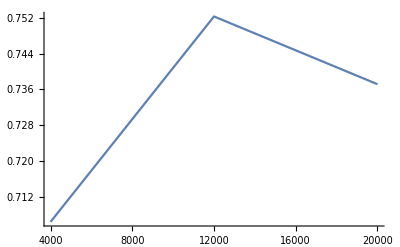

```mathematica
(* Here is the graph of the negative Precision of Random Forest with increasing training data, the data comes from several times testing *)
ListLinePlot[{{4000,0.706349},{12000,0.752311},{20000,0.737153}}]
```

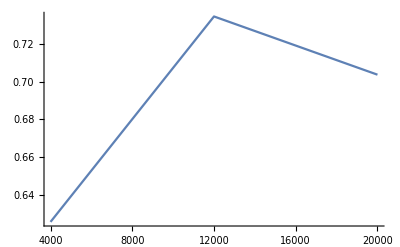

```mathematica
(* Here is the graph of the positive Recall of Random Forest with increasing training data, the data comes from several times testing *)
ListLinePlot[{{4000,0.625506},{12000,0.734653},{20000,0.703718}}]
```

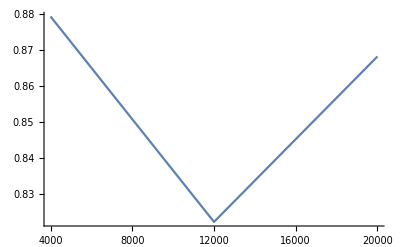

```mathematica
(* Here is the graph of the negative Recall of Random Forest with increasing training data, the data comes from several times testing *)
ListLinePlot[{{4000,0.879447},{12000,0.82222},{20000,0.868303}}]
```